## Globale Einstellungen

```mathematica
SetOptions[ListPlot,Joined->True,Frame->True,LabelStyle->{FontFamily->Times,FontSize->12,FontWeight->Bold}]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DataRange→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→True,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→800,ImageSizeRaw→Automatic,InterpolationOrder→None,Joined→True,LabelStyle→{FontFamily→Times,FontSize→12,FontWeight→Bold},MaxPlotPoints→∞,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotMarkers→None,PlotRange→Automatic,PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RotateLabel→True,Ticks→Automatic,TicksStyle→{}}

## Gasabsorption an Luft

```mathematica
Luft=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\00-Luft.DPT","Table"];
LuftNorm=Transpose[{Luft⟦All,1⟧,Luft⟦All,2⟧/Max[Luft⟦All,2⟧]}];
```

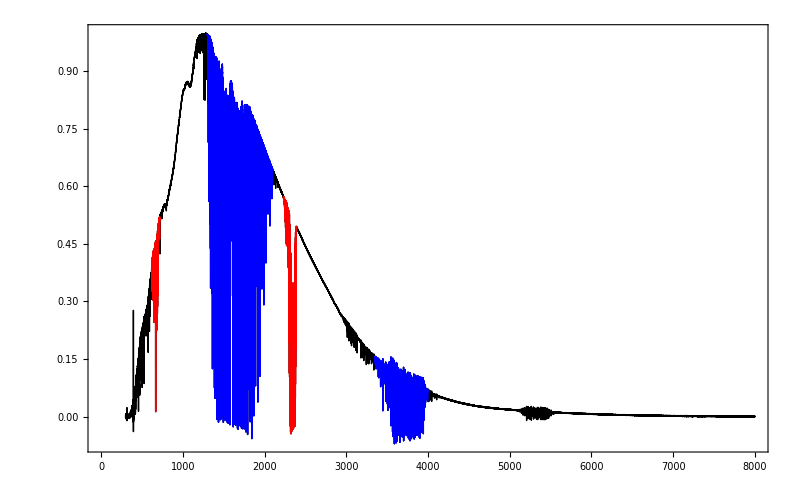

```mathematica
ListPlot[{Take[LuftNorm,{1,63875}],Take[LuftNorm,{46534,47859}],Take[LuftNorm,{60390,61220}],Take[LuftNorm,{33177,38574}],Take[LuftNorm,{48940,55578}]}, PlotStyle->{Black,Red,Red,Blue,Blue}]
```

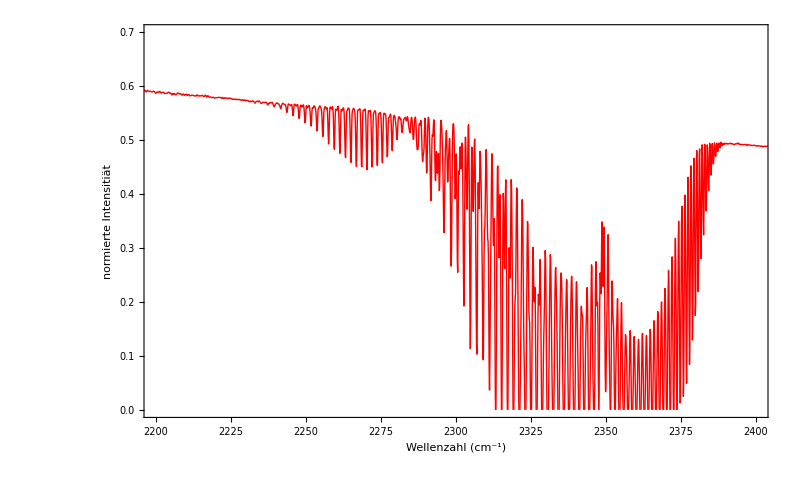

```mathematica
CO2a=ListPlot[LuftNorm,PlotRange->{{2200,2400},{0,0.7}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Red}]
```

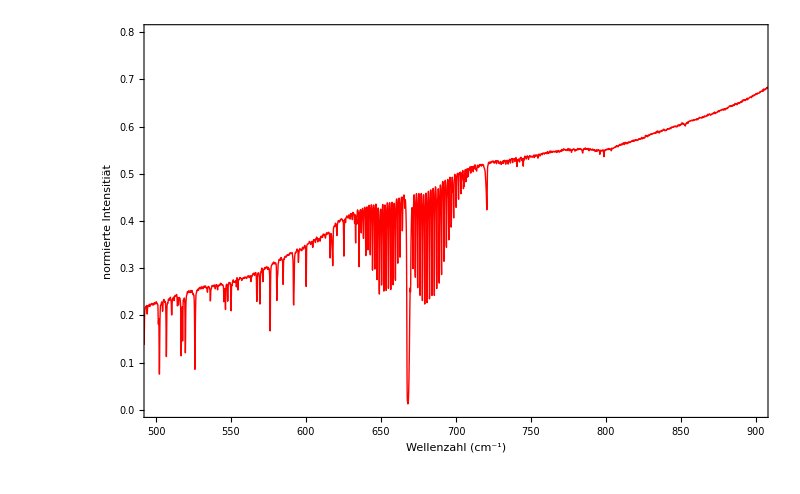

```mathematica
CO2b=ListPlot[LuftNorm,PlotRange->{{500,900},{0,0.8}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Red}]
```

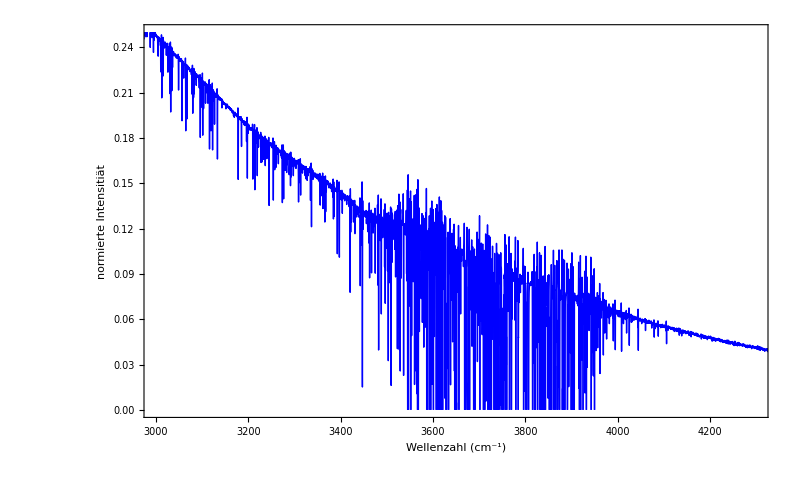

```mathematica
H2Oa=ListPlot[LuftNorm,PlotRange->{{3000,4300},{0,0.25}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue}]
```

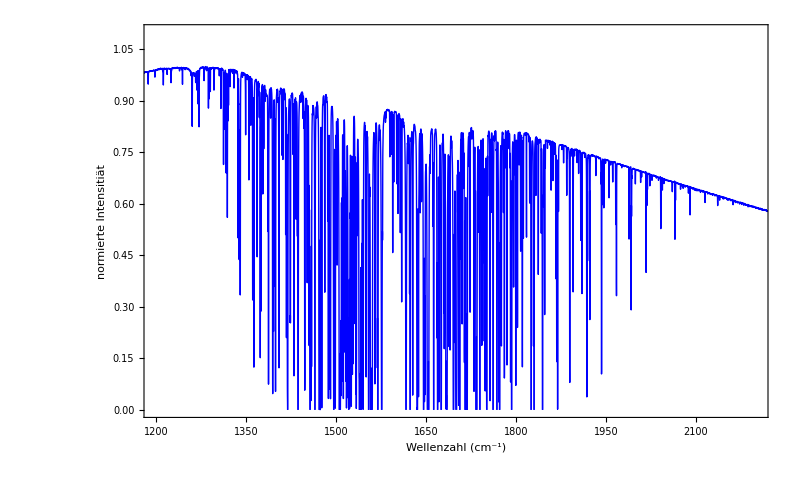

```mathematica
H2Ob=ListPlot[LuftNorm,PlotRange->{{1200,2200},{0,1.1}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue}]
```

## Signal-Rausch-Verhältnis

```mathematica
Rausch10=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\01-N10.DPT","Table"];
Rausch50=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\02-N50.DPT","Table"];
Rausch100=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\03-N100.DPT","Table"];
```

0.999916

0.000555222

0.0000314333

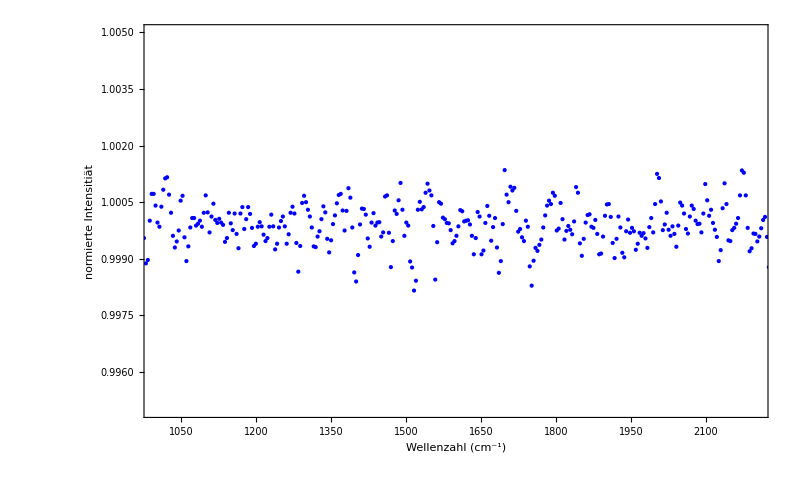

```mathematica
Mittelwert10=Mean[Rausch10[[1504;;1815]][[All,2]]]
Standardabweichung10=Sqrt[Mean[(Rausch10[[1504;;1815]][[All,2]]-Mean[Rausch10[[1504;;1815]][[All,2]]])^2]]
FehlerStandardabweichung10=Standardabweichung10/Sqrt[Length[Rausch10[[1504;;1815]]]]
PlotRausch10=ListPlot[Rausch10,PlotRange->{{1000,2200},{0.995,1.005}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue},Joined->False]
```

1.00005

0.000275646

0.0000156054

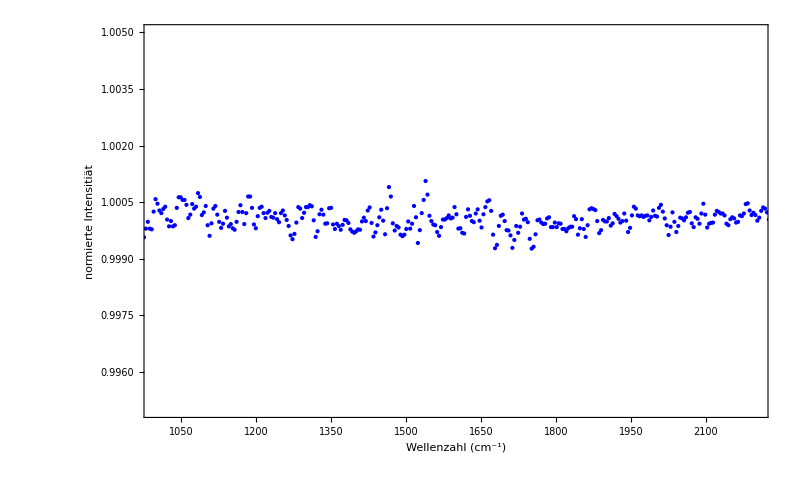

```mathematica
Mittelwert50=Mean[Rausch50[[1504;;1815]][[All,2]]]
Standardabweichung50=Sqrt[Mean[(Rausch50[[1504;;1815]][[All,2]]-Mean[Rausch50[[1504;;1815]][[All,2]]])^2]]
FehlerStandardabweichung50=Standardabweichung50/Sqrt[Length[Rausch10[[1504;;1815]]]]
PlotRausch50=ListPlot[Rausch50,PlotRange->{{1000,2200},{0.995,1.005}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue},Joined->False]
```

1.00035

0.000171068

9.68482×10^-6

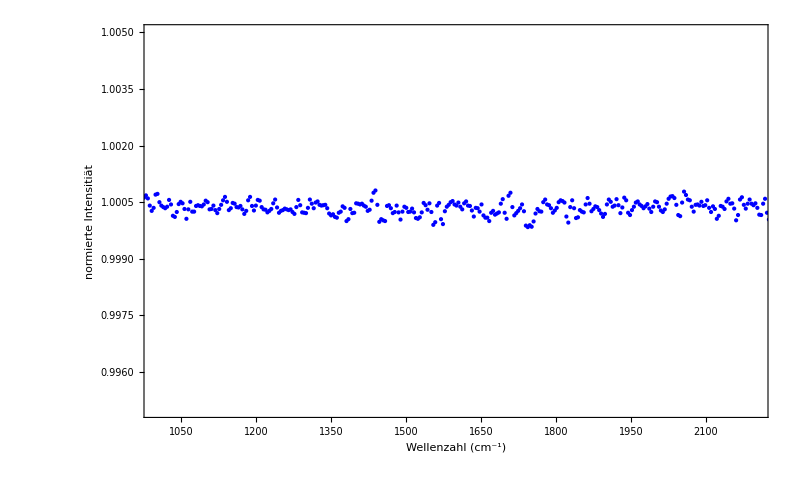

```mathematica
Mittelwert100=Mean[Rausch100[[1504;;1815]][[All,2]]]
Standardabweichung100=Sqrt[Mean[(Rausch100[[1504;;1815]][[All,2]]-Mean[Rausch100[[1504;;1815]][[All,2]]])^2]]
FehlerStandardabweichung100=Standardabweichung100/Sqrt[Length[Rausch100[[1504;;1815]]]]
PlotRausch100=ListPlot[Rausch100,PlotRange->{{1000,2200},{0.995,1.005}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue},Joined->False]
```

```mathematica
nsquare={{{1,Standardabweichung10*Sqrt[10]},ErrorBar[FehlerStandardabweichung10*Sqrt[10]]},
		  {{2,Standardabweichung50*Sqrt[50]},ErrorBar[FehlerStandardabweichung50*Sqrt[50]]},
		{{3,Standardabweichung100*Sqrt[100]},ErrorBar[FehlerStandardabweichung100*Sqrt[100]]}}
```

{{{1,0.00175577},ErrorBar[0.0000994007]},{{2,0.00194911},ErrorBar[0.000110347]},{{3,0.00171068},ErrorBar[0.0000968482]}}

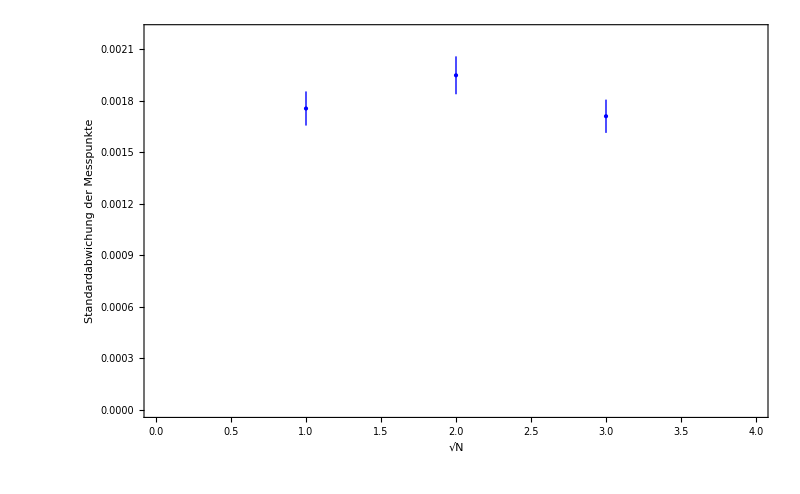

```mathematica
Needs["ErrorBarPlots`"];
nsqurePlot=ErrorListPlot[nsquare,PlotRange->{{0,4},{0,0.0022}},FrameLabel->{"√N","Standardabwichung der Messpunkte"},PlotStyle->{Blue},Joined->False]
```

```mathematica
nsquare={{{1/Sqrt[10],Standardabweichung10},ErrorBar[FehlerStandardabweichung10]},
		  {{1/Sqrt[50],Standardabweichung50},ErrorBar[FehlerStandardabweichung50]},
		{{1/Sqrt[100],Standardabweichung100},ErrorBar[FehlerStandardabweichung100]}}
```

{{{1/(√10),0.000555222},ErrorBar[0.0000314333]},{{1/(5 √2),0.000275646},ErrorBar[0.0000156054]},{{1/10,0.000171068},ErrorBar[9.68482×10^-6]}}

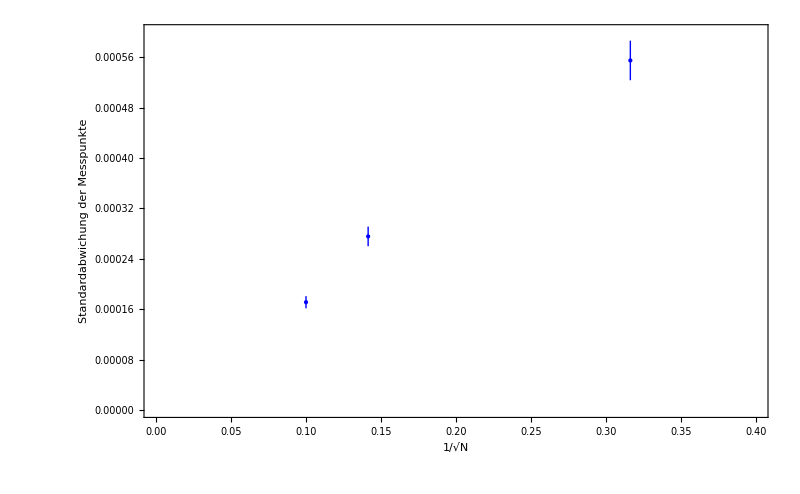

```mathematica
Needs["ErrorBarPlots`"];
nsqurePlot=ErrorListPlot[nsquare,PlotRange->{{0,0.4},{0,0.0006}},FrameLabel->{"1/√N","Standardabwichung der Messpunkte"},PlotStyle->{Blue},Joined->False]
```

## Bestimmung der Brechzahl

```mathematica
HrRGaAsundotiert=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\04-GaAs-undotiert.DPT","Table"];
HrRGaAsdotiert=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\05-GaAs-dotiert.DPT","Table"];
HrRSiundotiert=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\06-Si-undotiert.DPT","Table"];
```

GaAs undotiert

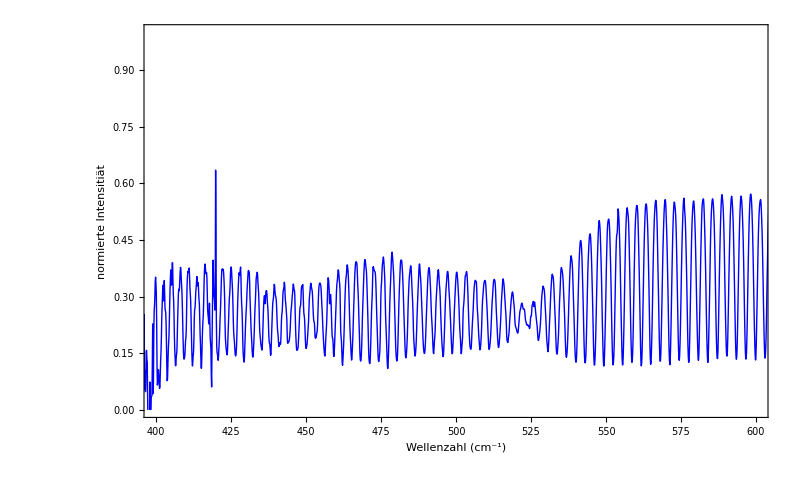
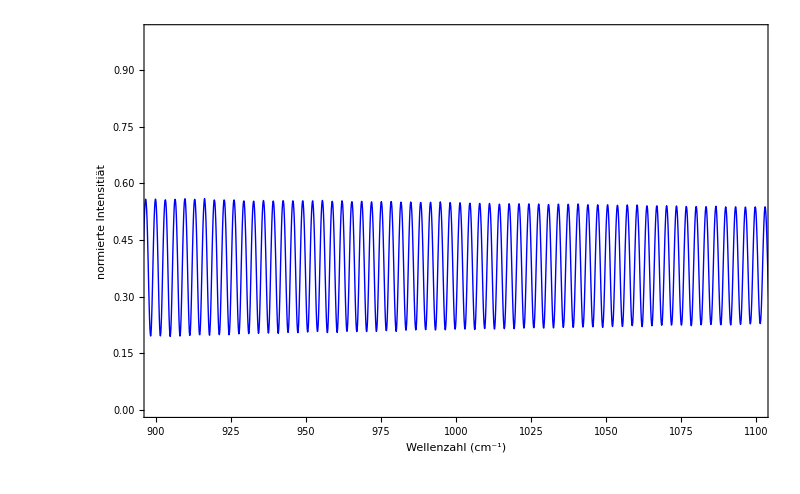
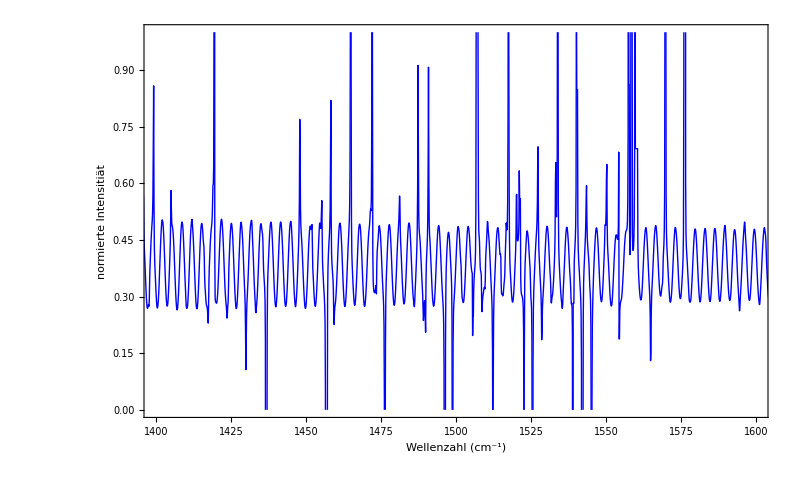
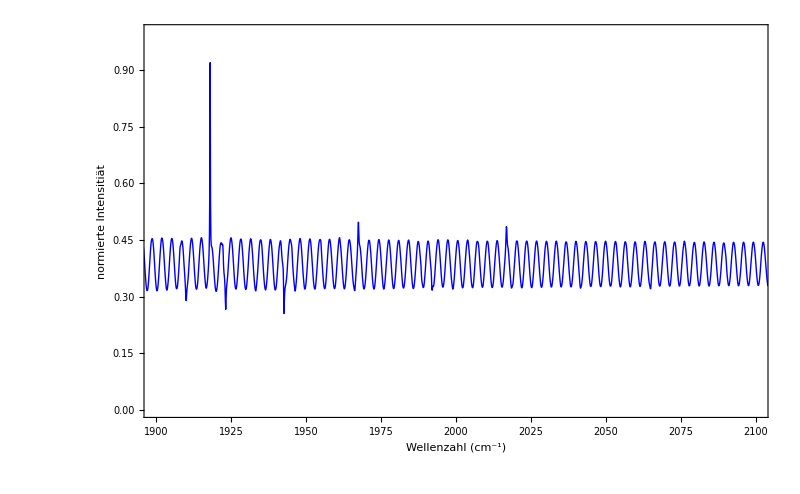
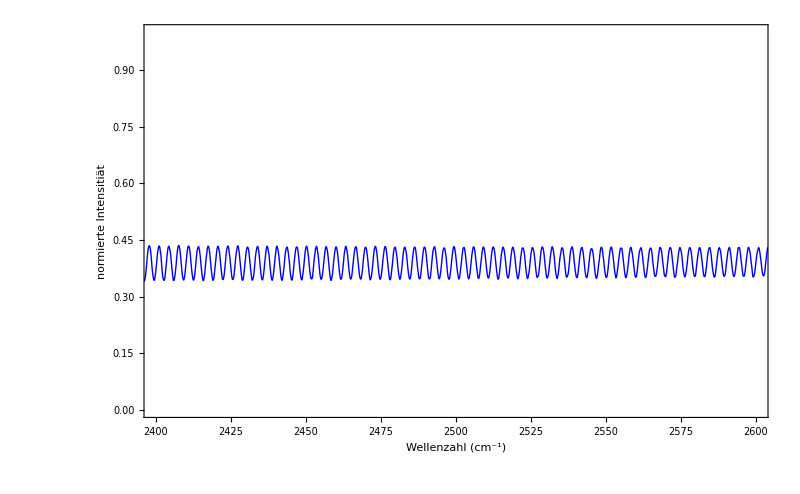
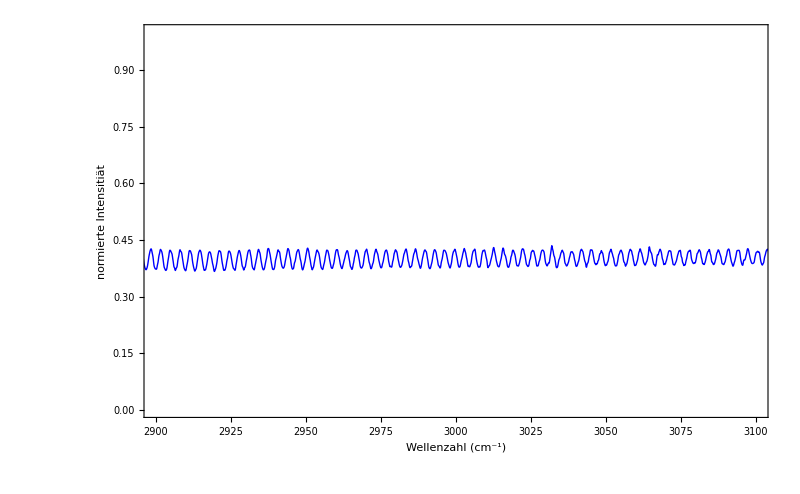
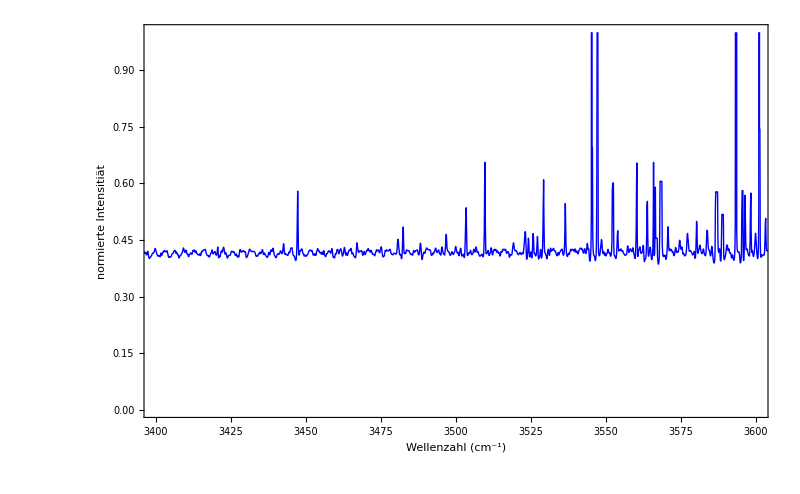
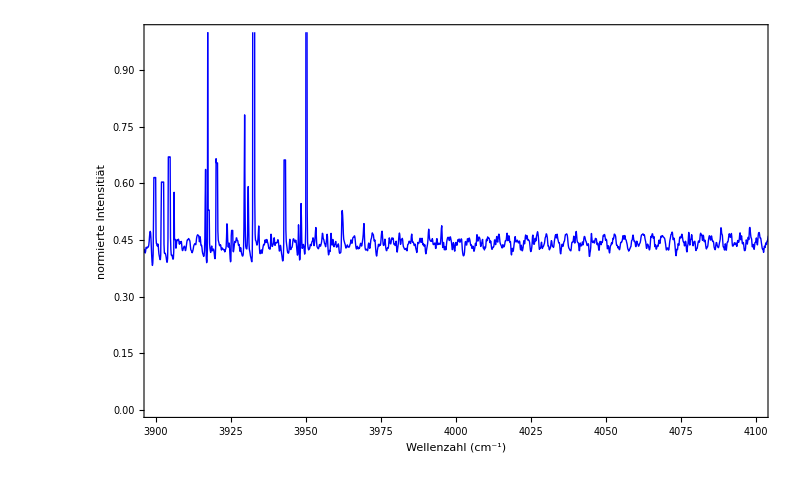

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
PlotHrRGaAsundotiert=Table[ListPlot[HrRGaAsundotiert,PlotRange->{ {i-100,i+100},{0,1}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue}],{i,500,5000,500}]
```

GaAs dotiert

```mathematica
PlotHrRGaAsdotiert=Table[ListPlot[HrRGaAsdotiert,PlotRange->{ {i-100,i+100},{0.1,0.4}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue}],{i,500,5000,500}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Si undotiert

```mathematica
PlotHrRSiundotiert=Table[ListPlot[HrRSiundotiert,PlotRange->{ {i-100,i+100},{0.1,0.7}},FrameLabel->{"Wellenzahl (cm^-1)","normierte Intensitiät"},PlotStyle->{Blue}],{i,500,5000,500}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## Breckzahlen und Extinktionskoefizienten

```mathematica
d=440*10^-4;
rg=((n-1)^2+κ^2)/((n+1)^2+κ^2);
Δrg1=0.0;
Δrg2=0.0;
β=4*π*Abs[κ]*ν;
transth=((1-rg-Δrg1)(1-rg-Δrg2)*Exp[-β*d])/(1-(rg-Δrg1)*(rg-Δrg2)*Exp[-2*β*d]);
reflth=rg-Δrg1+(((1-(rg+Δrg1))^2)* (rg-Δrg2)*Exp[-2*β*d])/(1-(rg-Δrg1)*(rg-Δrg2)*Exp[-2*β*d]);
```

## Fitten der Intrabandabsorption

```mathematica
RGaAsdot=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\08-R-GaAs-dotiert.DPT","Table"];
RSidot=Import["D:\\Git\\F-Praktikum\\FKO\\Rohdaten\\10-R-Si-dotiert.DPT","Table"];
ListPlot[RGaAsdot, PlotStyle->{Blue}]
ListPlot[RSidot, PlotStyle->{Blue}]
```

-Graphics-

-Graphics-

```mathematica
Clear[ref,βabs]
(*Eingabeparameter*)
Print["Trägerdichte in 10^18 cm^-3"]
ne=1.05
Print["Streuzeit in 10^-12 s"]
τ=0.1
Print["relative effektive Masse"]
meff=0.067
Print["relative Dielektrizitätskonstante"]
ϵ∞=3.22^2
Print["LO Phononenfrequenz in cm-1"]
νLO=292
Print["TO Phononenfrequenz in cm-1"]
νTO=268
Print["Phononendämpfungskonstante in cm-1"]
Γ=2.5
```

Trägerdichte in 10^18 cm^-3

1.05

Streuzeit in 10^-12 s

0.1

relative effektive Masse

0.067

relative Dielektrizitätskonstante

10.3684

LO Phononenfrequenz in cm-1

292

TO Phononenfrequenz in cm-1

268

Phononendämpfungskonstante in cm-1

2.5

```mathematica
(*Hochfrequenzleitfähigkeit in (Ωm)-1*)
σ=28202.2(ne*τ)/meff1/(1-ⅈ*0.188364*ν*τ);

(*Dielektrizitätsfunktion,  x = Skalierungsfaktor für Gitterbeitrag*)
ϵps[x_]:=ϵ∞(1+x*(νLO^2-νTO^2)/(νTO^2-ν^2-ⅈ*ν*Γ))+ⅈσ/(1.66818*ν);

(*Extinktionskoeffizient*)
ext[x_]:=Im[√ϵps[x]];

(*Brechzahl*)
brec[x_]:=Re[√ϵps[x]];

(*Absorptionskoeffizient*)
βabs[x_]:=4*π*ext[x]*ν;


Print["Plasmafrequenz in cm-1"]
νp=299.48√(ne/(meff*ϵ∞))

Print["Frequenz der oberen Plasmon-Phonon-Mode in cm-1"]
νpp=√(1/2(νLO^2+νp^2)+1/2√((νLO^2+νp^2)^2-4*νp^2*νTO^2))

Print["Frequenz der unteren Plasmon-Phonon-Mode in cm-1"]
νpm=√(1/2(νLO^2+νp^2)-1/2√((νLO^2+νp^2)^2-4*νp^2*νTO^2))

(*Reflexion am Halbraum*)
rh[x_]:=Abs[(√ϵps[x]-1)/(√ϵps[x]+1)]^2;

(*Reflexion einer planparallelen Schicht*)

ref[x_,d_]:=rh[x](1+Exp[-2*βabs[x]*d]-2*rh[x]*Exp[-2*βabs[x]*d])/(1-(rh[x]^2)*Exp[-2*βabs[x]*d]);


(*Einfluss der Schichtdicke d, ohne Gitterbeitrag*)
Plot[{rh[0],0.01+ref[0,640*10^-4],0.02+ref[0,440*10^-4],0.03+ref[0,240*10^-4]},{ν,1,2800},PlotRange->{0,1.1},FrameLabel->{"wave numbers (cm^-1)","Reflexion"},PlotLabel->"n-dot-GaAs, ϵ(ω) ohne Gitterbeitrag "]
```

Plasmafrequenz in cm-1

368.188

Frequenz der oberen Plasmon-Phonon-Mode in cm-1

399.944

Frequenz der unteren Plasmon-Phonon-Mode in cm-1

246.72

-Graphics-

```mathematica
(*Einfluss der Schichtdicke d, mit Gitterbeitrag*)
Plot[{rh[1],0.01+ref[1,640*10^-4],0.02+ref[1,440*10^-4],0.03+ref[1,240*10^-4]},{ν,1,2800},PlotRange->{0,1.1},FrameLabel->{"wave numbers (cm^-1)","Reflexion"},PlotLabel->"n-dot-GaAs, ϵ(ω) mit Gitterbeitrag "]
```

-Graphics-

```mathematica
Plot[ref[1,640*10^-4],{ν,1,2800},PlotRange->{0,1.1},FrameLabel->{"wave numbers (cm^-1)","Reflexion"},PlotLabel->"n-dot-GaAs, ϵ(ω) mit Gitterbeitrag "]
```

-Graphics-

Theorie und Experiment

## charakteristische Phononenfrequenz

```mathematica
(*Eingabeparameter*)
Print["Temperatur in Kelvin"]
T=300;
Print["Energielücke in cm-1"]
νg=8900
Print["Phononenenergie in cm-1"]
νph=450
Print["dimensionsloser Skalierungsfaktor"]
A=7500

(*Phononenbesetzungszahl*)
nph=1/(Exp[1.4397 νph/T]-1);

(*theoretischer Absorptionskoeffizient*)
βemm=A/ν^2*If[ν≥νg+νph,((ν-νg-νph)^2)*(nph+1),0];
βabs=A/ν^2*If[ν≥νg-νph,((ν-νg+νph)^2)*nph,0];
β=βemm+βabs;

(*experimenteller Absorptionskoeffizient*)
βexp=Interpolation[absorptionskoeffizient,InterpolationOrder->1]

Plot[{√βexp[ν] ν,√β*ν,√βemm*ν,√βabs*ν},{ν,8000,10500},FrameLabel->{"wave numbers (cm^-1)","√(β*SuperscriptBox[ν, 2]) (cm^(-3/2))"},PlotRange->{0,10^5},PlotLegend->{"experiment","√(β*SuperscriptBox[ν, 2])","√β_emm","√β_abs"}]
```

Temperatur in Kelvin

Energielücke in cm-1

8900

Phononenenergie in cm-1

450

dimensionsloser Skalierungsfaktor

7500

Interpolation::innd: First argument in absorptionskoeffizient does not contain a list of data and coordinates.

Interpolation[absorptionskoeffizient,InterpolationOrder→1]

Plot::optx: Unknown option PlotLegend in {√βexp[ν] ν, √β ν, √βemm ν, √βabs ν}, {ν, 8000, 10500}, FrameLabel → {.

Plot[{√βexp[ν] ν,√β ν,√βemm ν,√βabs ν},{ν,8000,10500},FrameLabel→{wave numbers (cm^-1),√(β*SuperscriptBox[ν, 2]) (cm^(-3/2))},PlotRange→{0,10^5},PlotLegend→{experiment,√(β*SuperscriptBox[ν, 2]),√β_emm,√β_abs}]

```mathematica
Clear[τ]
(*Eingabeparameter*)
Print["Trägerdichte in 10^18 cm^-3, hier: Gold"]
ne=5.9*10^4
Print["relative effektive Masse"]
meff=1
Print["relative Dielektrizitätskonstante"]
ϵs=1

(*Hochfrequenzleitfähigkeit in (Ωm)-1*)
σ=28202.2(ne*τ)/meff 1/(1-ⅈ*0.188364*ν*τ);

(*Dielektrizitätsfunktion*)
ϵ=ϵs+ⅈ σ/(1.66818*ν);

Print["Plasmafrequenz in cm-1"]
νp=299.48 √(ne/(meff*ϵs))

(*Reflexion am Halbraum*)
rhm=Abs[(√ϵ-1)/(√ϵ+1)]^2;

(*Reflexion eines Metalls, Halbraumgeometrie, Abhängigkeit von der Streuzeit*)
Plot[{rhm/.τ->0.1,rhm/.τ->0.01,rhm/.τ->0.001,rhm/.τ->0.0001},{ν,1,150000},PlotRange->{0,1.1},FrameLabel->{"wave numbers (cm^-1)","Reflexion"}]
```

Trägerdichte in 10^18 cm^-3, hier: Gold

59000.

relative effektive Masse

1

relative Dielektrizitätskonstante

1

Plasmafrequenz in cm-1

72743.4

-Graphics-

```mathematica
Plot[{rh[1],0.01+ref[1,640*10^-4],0.02+ref[1,440*10^-4],0.03+ref[1,240*10^-4]},{ν,1,2800},PlotRange->{0,1.1},FrameLabel->{"wave numbers (cm^-1)","Reflexion"},PlotLabel->"n-dot-GaAs, ϵ(ω) mit Gitterbeitrag "]
```

Plot::exclul: {(139351.\ Im[1/71824 + Times[« 2 »] + Times[« 2 »]] + Im[(0.  + 9.97452×10^8\ ⅈ)\ τ/ν\ (1 + Times[« 3 »])]) - 0, (139351.\ Im[1/71824 + Times[« 2 »] + Times[« 2 »]] + Im[(0.  + 9.97452×10^8\ ⅈ)\ τ/ν\ (1 + Times[« 3 »])]) - 0}
 must be a list of equalities or real-valued functions.

Plot::exclul: {(139351.\ Im[1/71824 + Times[« 2 »] + Times[« 2 »]] + Im[(0.  + 9.97452×10^8\ ⅈ)\ τ/ν\ (1 + Times[« 3 »])]) - 0, (139351.\ Im[1/71824 + Times[« 2 »] + Times[« 2 »]] + Im[(0.  + 9.97452×10^8\ ⅈ)\ τ/ν\ (1 + Times[« 3 »])]) - 0, (139351.\ Im[1/« 1 »] + Im[« 1 »/ν « 1 » « 1 »]) - 0, « 1 » « 1 » « 1 », (139351.\ Im[1/71824 + Times[« 2 »] + Times[« 2 »]] + Im[(0.  + « 21 »\ ⅈ)\ τ/ν\ (1 + Times[« 3 »])]) - 0, (139351.\ Im[1/71824 + Times[« 2 »] + Times[« 2 »]] + Im[(0.  + 9.97452×10^8\ ⅈ)\ τ/ν\ (1 + Times[« 3 »])]) - 0}
 must be a list of equalities or real-valued functions.

General::stop: Further output of Plot :: exclul will be suppressed during this calculation.

-Graphics-